Stopping Times

```mathematica
demandProcess[x0_,t_,μ_,σ_]:=x0 Exp[(μ-σ^2/2)t+σ RandomVariate[NormalDistribution[0,Sqrt[t]]]];
```

```mathematica
stopTime[timeStep_,xthreshold_,x0_,μ_,σ_]:=Module[{stop,t,X},
stop=0; (* hasn't stopped *)
t=0.001;
X={x0};
While[Last[X]<xthreshold,
X=Append[X,demandProcess[x0,t,μ,σ]];
t=t+timeStep];
t];
```

```mathematica
stopTimemod[timeStep_,xthreshold_,x0_,μ_,σ_,horizon_]:=Module[{stop,t,X},
t=0;
X={x0};
While[Last[X]<xthreshold &&t ≤horizon,
t=t+timeStep;
X=Append[X,demandProcess[x0,t,μ,σ]];
];
X=Append[X,Table[demandProcess[x0,t+timeStep*i,μ,σ],{i,horizon-t}]];
{t,Flatten@X}];
```

```mathematica
generalStopTime[Xmin_,Xmax_, xStep_,NsamplePaths_,timeStep_,xthreshold_,μ_,σ_]:=
Module[{x0=Xmin,
stop={},
X={}
},
While[x0≤Xmax,
stop=Append[stop,Table[stopTime[timeStep,xthreshold,x0,μ,σ],{i,1,NsamplePaths}]];
X=Append[X,Table[x0,{i,1,NsamplePaths}]];
x0=x0+xStep;
];
{X,stop}
];
```

```mathematica
estTau[x0_,threshold_]:=Module[{b},
Table[
b =Table[
stopTimemod[timeStep,(*xB[μ,σ,r,θ,k,α,δ]*) threshold@σ,x0,μ,σ,horizon],{i,NsamplePaths}];
(*Print["Tempos de paragem=",First/@b];*)
If[Count[First/@b,horizon+timeStep] >0,
Print["(σ, # unended sample paths) = ",{σ,Count[First/@b,horizon+timeStep]}]
];
Mean[First/@b],
{σ,0.01,σMax,0.01}]
];
```

```mathematica
hist[timeStep_,xfunc_,x0_,μ_,σ_,horizon_,NsamplePaths_,color_]:=Module[{b,xthreshold=xfunc@σ},
b =Table[
stopTimemod[timeStep,xthreshold,x0,μ,σ,horizon],{i,NsamplePaths}];
{Histogram[First/@b,20,
 ChartStyle->color,AxesLabel->{"τ"," "}],First/@b, ShapiroWilkTest[First/@b,"TestDataTable"]}
];
```

## Prob 1

```mathematica
d1[μ_,σ_,r_]:=1/2-μ/σ^2+Sqrt[(1/2-μ/σ^2)^2+2r/σ^2]; 
xB[μ_,σ_,r_,θ_,k_,α_,δ_]:=(d1[μ,σ,r])/(d1[μ,σ,r]-1) δ (r-μ)/(θ- α k);
xC[μ_,σ_,r_,θ_,δ_]:=(d1[μ,σ,r]+1)/(d1[μ,σ,r]-1) δ (r-μ)/θ;
Kopt[μ_,r_,θ_,α_,δ_,x_]:=(θ x-δ(r-μ))/(2 α x);
```

### Benchmark & Capacity Optimization Models:

{xB,xC}={0.0128124,0.0190623}

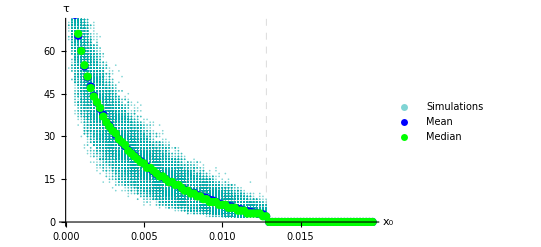
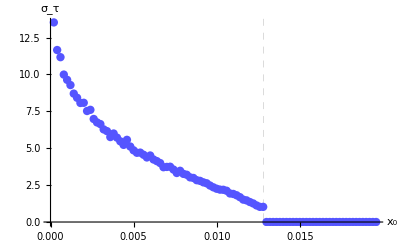
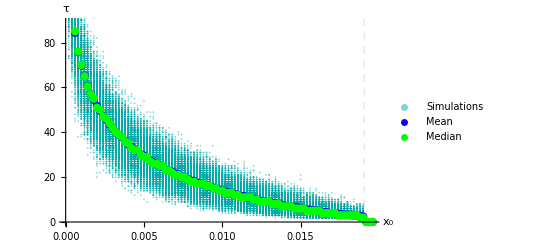
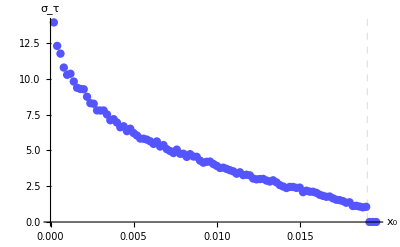

```mathematica
SeedRandom[1];
Module[
{σ=0.1,
μ=0.03,
r=0.05,
δ=2,
α=0.01,
θ=10,
k=100,
xStep=0.0002,
Xmin=0.0002,
Xmax,
NsamplePaths=1000,
timeStep=1,
trialBM,
trialCOM},
Print["{xB,xC}=",{xB[μ,σ,r,θ,k,α,δ],xC[μ,σ,r,θ,δ]}];
Xmax=Max[{xC[μ,σ,r,θ,δ],xB[μ,σ,r,θ,k,α,δ]}]+3*xStep;
trialBM=generalStopTime[Xmin,Xmax, xStep,NsamplePaths,timeStep,xB[μ,σ,r,θ,k,α,δ],μ,σ];
trialCOM=generalStopTime[Xmin,Xmax, xStep,NsamplePaths,timeStep,xC[μ,σ,r,θ,δ],μ,σ];
{Show[
(* Benchmark Model *)
(* Mean & Median *)
ListPlot[{Transpose@{Flatten@trialBM[[1]],Flatten@trialBM[[2]]},Transpose@{Mean/@trialBM[[1]],Mean/@trialBM[[2]]} ,Transpose@{Median/@trialBM[[1]],Median/@trialBM[[2]]}},
PlotStyle->{{Darker[Cyan],Opacity[.5],PointSize[0.003]},{Blue,PointSize[0.015]},{Green,PointSize[0.015]}} ,
PlotLegends->Placed[{"Simulations","Mean","Median"},{Right,Top}],
AxesLabel->{"x_0","τ"},
GridLines->{{{xB[μ,σ,r,θ,k,α,δ],Dashed}},{}}
]
],
(* Standard deviation *)
 ListPlot[Transpose@{Mean/@trialBM[[1]],StandardDeviation/@trialBM[[2]]},PlotStyle->{Lighter[Blue],PointSize[0.015]},
AxesLabel->{"x_0","σ_τ"},
GridLines->{{{xB[μ,σ,r,θ,k,α,δ],Dashed}},{}}],

(* Capacity Optimization Model *)
(* Mean & Median *)
ListPlot[{Transpose@{Flatten@trialCOM[[1]],Flatten@trialCOM[[2]]},Transpose@{Mean/@trialCOM[[1]],Mean/@trialCOM[[2]]} ,Transpose@{Median/@trialCOM[[1]],Median/@trialCOM[[2]]}},
PlotStyle->{{Darker[Cyan],Opacity[.5],PointSize[0.003]},{Blue,PointSize[0.015]},{Green,PointSize[0.015]}} ,
PlotLegends->Placed[{"Simulations","Mean","Median"},{ Right,Top}],
AxesLabel->{"x_0","τ"},
GridLines->{{{xC[μ,σ,r,θ,δ],Dashed}},{}}
],
(* Standard deviation *)
 ListPlot[Transpose@{Mean/@trialCOM[[1]],StandardDeviation/@trialCOM[[2]]},PlotStyle->{Lighter[Blue],PointSize[0.015]},
AxesLabel->{"x_0","σ_τ"},
GridLines->{{{xC[μ,σ,r,θ,δ],Dashed}},{}}]
}
]
```

#### Variance analysis

{xB,xC}={0.0128124,0.0190623}

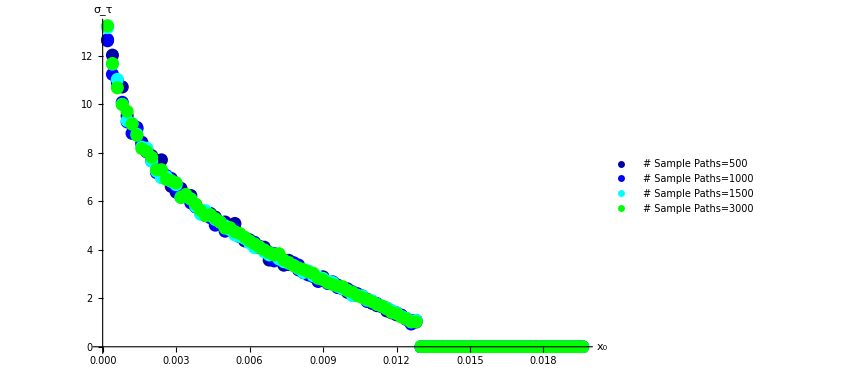
{-Graphics-,# Sample Paths | 500 | 1000 | 1500 | 3000
 Running Time (s)  | 8 | 16 | 25 | 49}

```mathematica
Module[
{σ=0.1,
μ=0.03,
r=0.05,
δ=2,
α=0.01,
θ=10,
k=100,
xStep=0.0002,
Xmin=0.0002,
Xmax,
timeStep=1},
Print["{xB,xC}=",{xB[μ,σ,r,θ,k,α,δ],xC[μ,σ,r,θ,δ]}];
Xmax=Max[{xC[μ,σ,r,θ,δ],xB[μ,σ,r,θ,k,α,δ]}]+3*xStep;
trialBM500=AbsoluteTiming@generalStopTime[Xmin,Xmax, xStep,500(*NsamplePaths*),timeStep,xB[μ,σ,r,θ,k,α,δ],μ,σ];
trialBM1000=AbsoluteTiming@generalStopTime[Xmin,Xmax, xStep,1000(*NsamplePaths*),timeStep,xB[μ,σ,r,θ,k,α,δ],μ,σ];
trialBM1500=AbsoluteTiming@generalStopTime[Xmin,Xmax, xStep,1500(*NsamplePaths*),timeStep,xB[μ,σ,r,θ,k,α,δ],μ,σ];
trialBM3000=AbsoluteTiming@generalStopTime[Xmin,Xmax, xStep,3000(*NsamplePaths*),timeStep,xB[μ,σ,r,θ,k,α,δ],μ,σ];

(* Standard deviation *)
{
 ListPlot[{Transpose@{Mean/@trialBM500[[2,1]],StandardDeviation/@trialBM500[[2,2]]},
Transpose@{Mean/@trialBM1000[[2,1]],StandardDeviation/@trialBM1000[[2,2]]},
Transpose@{Mean/@trialBM1500[[2,1]],StandardDeviation/@trialBM1500[[2,2]]},
Transpose@{Mean/@trialBM3000[[2,1]],StandardDeviation/@trialBM3000[[2,2]]}
},
PlotStyle->{{Darker[Blue],PointSize[0.015]},{Blue,PointSize[0.015]},{Cyan,PointSize[0.015]},{Green,PointSize[0.015]}},
AxesLabel->{"x_0","σ_τ"},
PlotLegends->Placed[{"# Sample Paths=500 "  ,"# Sample Paths=1000 ","# Sample Paths=1500 ","# Sample Paths=3000 "},{Right,Top}]
],

Δ={500,1000, 1500, 3000};
time=Round@{trialBM500[[1]],trialBM1000[[1]],trialBM1500[[1]],trialBM3000[[1]]};
Grid[{
 Join[{"# Sample Paths"},Δ],
Join[{" Running Time (s) "},time]
},
Dividers->{{2->True},{1->True,2->True,-1->True}}
]
}
]
```

### Volatility sensibility

```mathematica
μ=0.03;
r=0.05;
δ=2;
α=0.01;
θ=10;
k=100;
NsamplePaths=500;
timeStep=1;
(*x0={0.001,0.01};*)

σMax=0.5;
horizon=1500;
```

Plots para σ∈(0.001,0.5) considerando x0∈{0.001,0.01} :

```mathematica
estTauB001=estTau[0.001,Function[σ,xB[μ,σ,r,θ,k,α,δ]]];
estTauB01=estTau[0.01,Function[σ,xB[μ,σ,r,θ,k,α,δ]]];
estTauC001=estTau[0.001,Function[σ,xC[μ,σ,r,θ,δ]]];
estTauC01=estTau[0.01,Function[σ,xC[μ,σ,r,θ,δ]]];
```

(σ, # unended sample paths) = {0.38,2}

(σ, # unended sample paths) = {0.39,9}

(σ, # unended sample paths) = {0.4,7}

(σ, # unended sample paths) = {0.41,20}

(σ, # unended sample paths) = {0.42,35}

(σ, # unended sample paths) = {0.43,53}

(σ, # unended sample paths) = {0.44,77}

(σ, # unended sample paths) = {0.45,100}

(σ, # unended sample paths) = {0.46,124}

(σ, # unended sample paths) = {0.47,157}

(σ, # unended sample paths) = {0.48,166}

(σ, # unended sample paths) = {0.49,195}

(σ, # unended sample paths) = {0.5,229}

$Aborted

$Aborted

(σ, # unended sample paths) = {0.43,1}

(σ, # unended sample paths) = {0.44,1}

(σ, # unended sample paths) = {0.46,5}

(σ, # unended sample paths) = {0.47,7}

(σ, # unended sample paths) = {0.48,8}

(σ, # unended sample paths) = {0.49,16}

(σ, # unended sample paths) = {0.5,18}

```mathematica
{
(* Mean optimal investment times *)
ListPlot[{Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauB001},
Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauB01},
Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauC001},
Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauC01}},
PlotLegends->Placed[{"Mean(τ_B) & x_0=0.001","Mean(τ_B) & x_0=0.01",
"Mean(τ_C) & x_0=0.001",
"Mean(τ_C) & x_0=0.01"},{Left,Top}],
AxesLabel->{"σ","Time units"},
Joined->True,
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Yellow,Darker[Yellow,0.2]},
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
],
(* Demand thresholds *)
Plot[{xB[μ,σ,r,θ,k,α,δ],xC[μ,σ,r,θ,δ]},{σ,0.01,σMax},
AxesOrigin->{0,0},
PlotLegends->Placed[{"x_B^*","x_C^*"},{Left,Top}],
AxesLabel->{"σ","x"}],
Plot[Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]],{σ,0.01,σMax},
AxesOrigin->{0,0},
AxesLabel->{"σ","K^*"},
PlotStyle->Brown],
ListPlot[
{
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTauB001,1]-Drop[estTauB001,-1])},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTauB01,1]-Drop[estTauB01,-1])},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTauC001,1]-Drop[estTauC001,-1])},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTauC01,1]-Drop[estTauC01,-1])},
Table[{σ+0.01,(xB[μ,σ+0.01,r,θ,k,α,δ]-xB[μ,σ,r,θ,k,α,δ])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(xC[μ,σ+0.01,r,θ,δ]-xC[μ,σ,r,θ,δ])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(Kopt[μ,r,θ,α,δ,xC[μ,σ+0.01,r,θ,δ]]-Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]])},{σ,0.01,σMax-0.01,0.01}]
},
(* % variation *)
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Yellow,Darker[Yellow,0.2],Lighter[Blue,0.3],Lighter[Orange,0.2],Brown},
PlotLegends->Placed[{"Mean(τ_B) & x_0=0.001","Mean(τ_B) & x_0=0.01",
"Mean(τ_C) & x_0=0.001",
"Mean(τ_C) & x_0=0.01",
"x_B^*","x_C^*","K^*" },{Left,Top}],
AxesLabel->{"σ","% variation"},
Joined->True,
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
]
}
```

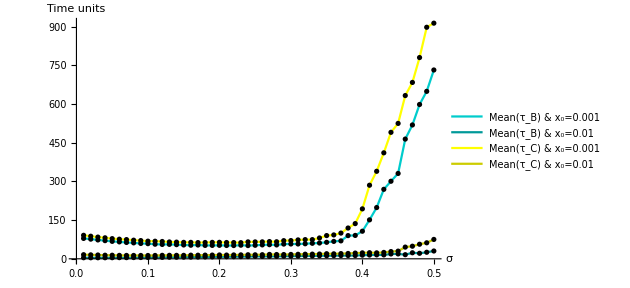
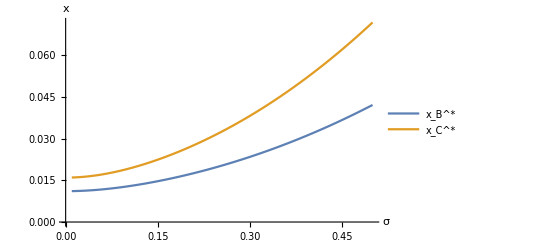
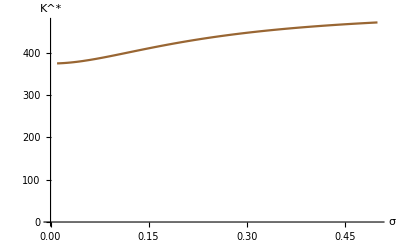
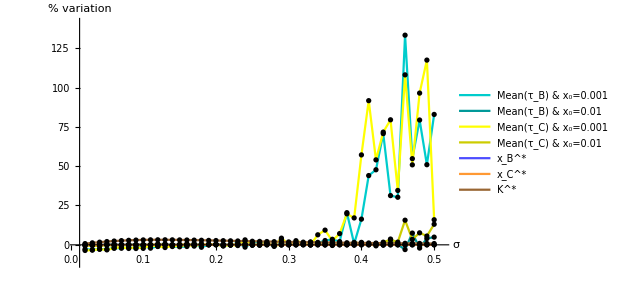

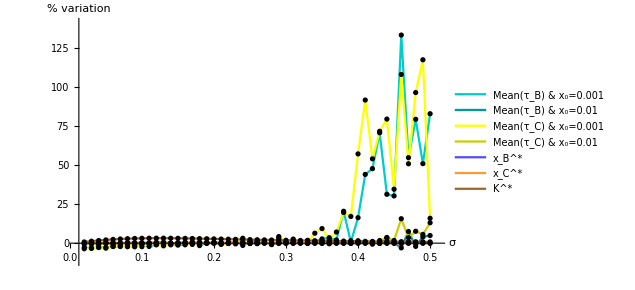
```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
(* % varitation up to σ=0.35 *)
Module[{σMax=0.35},
ListPlot[
{
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB001,1]-Drop[estTauB001,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB01,1]-Drop[estTauB01,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauC001,1]-Drop[estTauC001,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauC01,1]-Drop[estTauC01,-1]),(σMax-0.01)/0.01]},
Table[{σ+0.01,(xB[μ,σ+0.01,r,θ,k,α,δ]-xB[μ,σ,r,θ,k,α,δ])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(xC[μ,σ+0.01,r,θ,δ]-xC[μ,σ,r,θ,δ])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(Kopt[μ,r,θ,α,δ,xC[μ,σ+0.01,r,θ,δ]]-Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]])},{σ,0.01,σMax-0.01,0.01}]
},
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Yellow,Darker[Yellow,0.2],Lighter[Blue,0.3],Lighter[Orange,0.2],Brown},
PlotLegends->Placed[{"Mean(τ_B) & x_0=0.001","Mean(τ_B) & x_0=0.01",
"Mean(τ_C) & x_0=0.001",
"Mean(τ_C) & x_0=0.01",
"x_B^*","x_C^*","K^*" },{Scaled[{0,0.5}], {0, 0.5}}],
AxesLabel->{"σ","% variation"},
Joined->True,
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
]
]
```

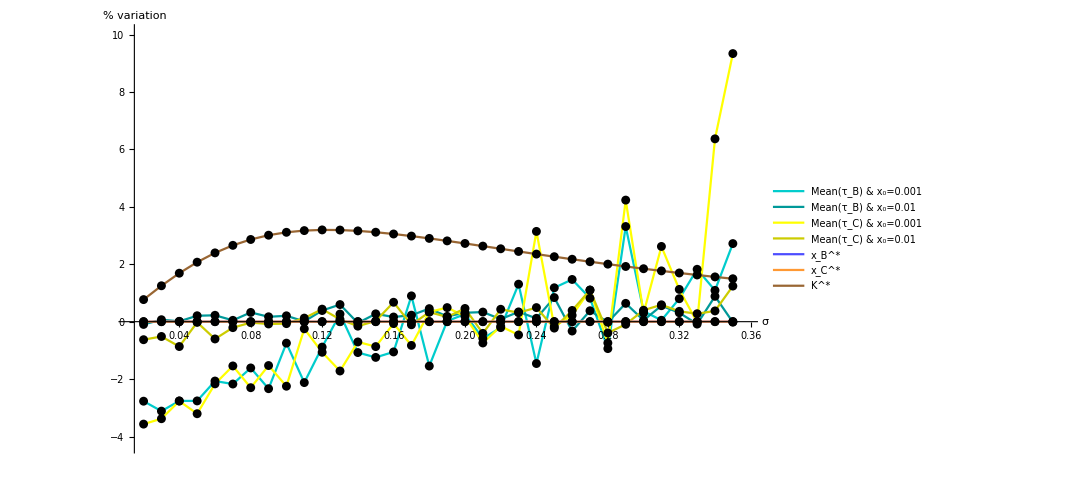

Tabela representativa:

```mathematica
(* Usar sse avaliar a value function *)
h[x_,r_,μ_,σ_,θ_,α_,δ_,k_]:=(θ- α k) k *x/(r-μ)-δ k;
aB[x_,μ_,σ_,r_,θ_,k_,α_,δ_]:=((θ- α k) k *x/(r-μ)-δ k)*x^(-d1[μ,σ,r]);
hC[x_,r_,μ_,σ_,θ_,α_,δ_]:=(x θ-δ (r-μ))^2/(4 α (r-μ)x);
aC[x_,μ_,σ_,r_,θ_,α_,δ_]:=(x θ-δ (r-μ))^2/(4 α (r-μ)x)*x^(-d1[μ,σ,r]);

FxB[x_,r_,μ_,σ_,θ_,α_,δ_,k_]:=If[x<xB[μ,σ,r,θ,k,α,δ],
aB[xB[μ,σ,r,θ,k,α,δ],μ,σ,r,θ,k,α,δ]*x^(d1[μ,σ,r]),
h[x,r,μ,σ,θ,α,δ,k]];
FxC[x_,r_,μ_,σ_,θ_,α_,δ_]:=If[x<xC[μ,σ,r,θ,δ],
aC[xC[μ,σ,r,θ,δ],μ,σ,r,θ,α,δ]*x^(d1[μ,σ,r]),
hC[x,r,μ,σ,θ,α,δ]];
```

```mathematica
Δ=Table[i,{i,0.05,0.4,0.05}];
part=Table[σ,{σ,0.01,σMax,0.01}];
Grid[{
 Join[{"x_0"," σ "},Δ],
Join[{" ", "K^*"},Map[Function[σ,NumberForm[Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]],5]],Δ]],

Join[{" ", "x_B^*"},Map[Function[σ,NumberForm[xB[μ,σ,r,θ,k,α,δ],2]],Δ]],
Join[{" ", "x_C^*"},Map[Function[σ,NumberForm[xC[μ,σ,r,θ,δ],2]],Δ]],

Join[{0.001, "OverBar[τ_B]"},N@Flatten@Map[Function[elem,estTauB001[[Flatten@Position[part,elem]]]],Δ]],
Join[{0.001, "OverBar[τ_C]"},N@Flatten@Map[Function[elem,estTauC001[[Flatten@Position[part,elem]]]],Δ]],
(*Prepend[Map[Function[σ,NumberForm[FxB[0.001,r,μ,σ,θ,α,δ,k],2]],Δ],"F_B"],
Prepend[Map[Function[σ,NumberForm[FxC[0.001,r,μ,σ,θ,α,δ],2]],Δ],"F_C"],*)

Join[{0.01, "OverBar[τ_B]"},N@Flatten@Map[Function[elem,estTauB01[[Flatten@Position[part,elem]]]],Δ]],
Join[{0.01, "OverBar[τ_C]"},N@Flatten@Map[Function[elem,estTauC01[[Flatten@Position[part,elem]]]],Δ]]
(*Prepend[Map[Function[σ,NumberForm[FxB[0.01,r,μ,σ,θ,α,δ,k],2]],Δ],"F_B"],
Prepend[Map[Function[σ,NumberForm[FxC[0.01,r,μ,σ,θ,α,δ],2]],Δ],"F_C"]*)
},
Dividers->{{2->True,3->True},{1->True,2->True,-5->True,-3->True,-1->True}}
]
```

x_0 |  σ  | 0.05 | 0.1 | 0.15 | 0.2 | 0.25 | 0.3 | 0.35 | 0.4
  | K^* | 381.04 | 395.08 | 410.92 | 425.39 | 437.62 | 447.66 | 455.8 | 462.41
  | x_B^* | 0.012 | 0.013 | 0.015 | 0.017 | 0.02 | 0.023 | 0.027 | 0.032
  | x_C^* | 0.017 | 0.019 | 0.022 | 0.027 | 0.032 | 0.038 | 0.045 | 0.053
0.001 | OverBar[τ_B] | 66.924 | 58.348 | 53.796 | 52.042 | 52.658 | 52.734 | 62.532 | 136.436
0.001 | OverBar[τ_C] | 79.19 | 69.346 | 64.95 | 62.368 | 66.044 | 69.63 | 83.046 | 176.542
0.01 | OverBar[τ_B] | 4.348 | 5.366 | 6.5 | 7.368 | 9.318 | 10.266 | 11.876 | 13.502
0.01 | OverBar[τ_C] | 13.736 | 12.992 | 13.474 | 14.406 | 15.68 | 17.524 | 20.45 | 21.984

### Histograma

```mathematica
μ=0.03;
r=0.05;
δ=2;
α=0.01;
θ=10;
k=100;
NsamplePaths=500;
timeStep=1;
(*x0={0.001,0.01};*)

σMax=0.5;
horizon=1500;
```

```mathematica
hist[timeStep_,xfunc_,x0_,μ_,σ_,horizon_,NsamplePaths_,color_]
```

#### x = 0.001

```mathematica
xB[μ,0.001,r,θ,k,α,δ]
```

0.0111113

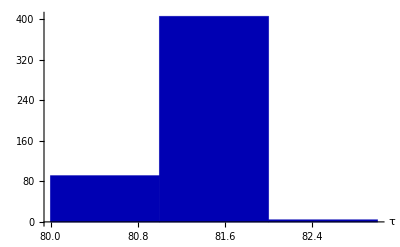
{-Graphics-,{81,81,81,81,81,81,81,81,81,81,81,81,81,80,81,81,81,81,81,81,81,81,80,81,81,81,81,81,81,80,81,81,80,81,81,81,81,81,81,81,81,81,80,81,81,81,81,81,81,81,81,81,80,81,81,81,81,80,81,80,80,81,81,81,81,81,80,80,81,80,81,81,81,80,81,81,80,81,81,80,81,81,81,81,81,81,81,81,81,81,81,81,82,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,80,81,81,81,81,81,81,81,81,81,81,80,81,81,80,81,81,81,81,81,81,81,80,80,81,81,81,81,81,81,81,81,80,81,81,81,81,81,81,81,81,81,81,81,81,80,81,80,81,80,81,81,81,81,81,82,81,81,81,81,81,80,80,81,81,81,81,81,81,81,80,81,81,80,81,80,81,81,80,81,82,81,81,81,81,80,81,81,80,81,80,81,81,81,80,81,80,81,81,81,80,80,81,81,80,81,81,81,81,80,80,81,80,81,80,81,81,81,80,81,81,81,81,81,81,81,81,81,80,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,80,81,81,81,81,80,81,80,81,81,81,81,81,81,80,81,81,80,81,81,81,80,81,80,80,81,81,81,81,81,81,81,81,81,80,81,81,80,81,81,81,81,81,81,81,82,80,81,81,80,81,81,81,81,81,80,81,81,81,81,81,81,80,81,81,80,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,80,80,81,81,80,81,81,81,81,81,81,81,81,81,81,81,81,81,81,80,81,81,81,81,81,81,81,80,81,81,81,81,81,81,80,81,80,81,81,81,81,81,81,81,81,81,81,80,81,81,81,81,81,81,81,81,81,81,81,80,80,81,80,81,81,81,80,81,81,81,81,81,81,81,81,81,81,81,81,81,81,80,81,81,81,80,81,80,81,81,81,81,81,81,81,80,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,80,81,81,81,81,80,81,81,81,81,80,81,80,80,81,81,81,81,81,80,81,81,81,80,80,81,81,80,81,81,81,81,81,81,80,81,81,81,80,81,81,80,81,80,80,81,80,81,80,81,81}}

```mathematica
hist[timeStep,Function[σ,xB[μ,σ,r,θ,k,α,δ]],0.001,μ,0.001,horizon,NsamplePaths,Darker[Blue,.3]]
```

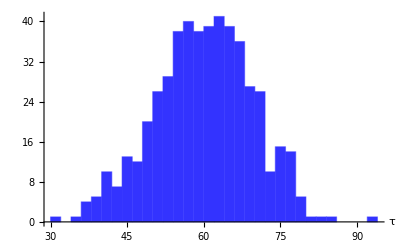
{-Graphics-,{58,55,57,59,65,69,59,58,53,48,59,56,56,46,63,64,50,58,56,56,70,55,67,60,71,66,48,79,63,69,53,70,53,67,36,59,69,66,46,41,57,50,62,62,37,74,45,49,75,45,58,75,64,64,54,61,82,65,71,40,62,55,53,68,79,65,64,41,55,56,55,68,56,58,46,53,56,61,47,55,75,70,67,63,53,62,72,38,54,69,43,64,71,57,62,77,60,61,53,56,61,64,55,59,65,50,58,63,45,63,59,76,44,73,69,39,36,74,58,68,50,68,51,66,45,59,40,59,48,60,66,62,49,54,56,67,53,31,58,71,70,63,49,56,41,59,74,50,74,38,62,71,67,58,67,54,50,67,48,65,68,68,57,71,58,67,59,53,62,84,55,62,78,65,56,70,77,59,56,62,67,65,64,52,66,50,55,72,64,44,76,59,73,38,53,56,59,56,56,61,66,66,63,60,70,53,51,48,62,76,68,51,54,65,58,75,54,71,61,65,68,80,66,53,46,60,62,60,67,49,59,65,55,57,69,44,59,56,93,45,41,62,54,55,64,43,56,72,62,61,60,44,55,37,48,49,59,69,41,63,74,55,51,54,64,65,49,54,61,67,77,63,62,66,76,73,64,61,49,58,52,76,67,60,53,65,59,69,65,67,69,55,50,60,58,61,40,67,43,59,43,51,56,64,69,68,53,43,71,67,48,62,55,46,45,62,61,71,73,56,58,57,54,49,60,77,76,75,65,63,53,55,60,67,58,57,56,41,52,67,63,64,64,62,51,60,44,67,71,60,54,62,42,61,62,71,68,76,63,47,50,64,70,74,67,59,69,72,77,52,55,58,54,52,57,76,68,66,65,70,50,76,57,68,61,47,70,52,72,61,50,50,68,75,40,56,66,57,66,67,63,51,56,62,57,50,52,63,68,57,50,43,61,51,53,48,74,71,67,52,54,62,47,63,51,61,56,64,61,64,64,54,57,48,48,54,55,61,68,54,62,60,60,47,65,63,60,49,53,49,65,60,46,70,68,51,59,52,71,59,52,60,74,47,50,54,57,35,65,53,64,73,65,44,39,54,55,70,56,55,74,64,70,79,66,62,57,58,66,79,62,61,61,56,50,45,53,61,70,67}, | Statistic | P-Value
Shapiro-Wilk | 0.996135 | 0.264044}

```mathematica
hist[timeStep,Function[σ,xB[μ,σ,r,θ,k,α,δ]],0.001,μ,0.1,horizon,NsamplePaths,Lighter[Blue, 0.2]]
```

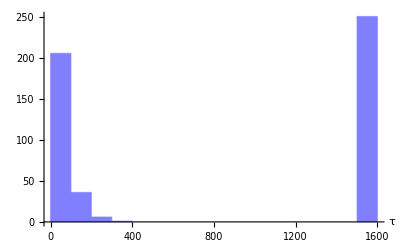
{-Graphics-,{1501,9,1501,1501,1501,108,1501,12,46,71,1501,44,28,12,1501,1501,28,1501,85,1501,49,1501,1501,1501,45,91,1501,22,56,42,1501,1501,1501,23,35,40,83,21,62,1501,1501,1501,1501,1501,36,28,26,1501,1501,1501,1501,79,1501,46,44,1501,1501,1501,1501,1501,1501,1501,159,1501,1501,1501,1501,35,24,77,1501,75,31,39,56,1501,94,19,1501,45,1501,96,52,74,1501,1501,102,43,1501,65,31,1501,99,1501,1501,97,1501,1501,1501,1501,55,1501,244,33,1501,84,46,1501,1501,166,33,1501,1501,1501,1501,84,1501,1501,1501,1501,158,1501,37,22,71,1501,101,1501,1501,1501,1501,69,1501,1501,1501,1501,1501,1501,1501,1501,21,149,56,1501,1501,1501,1501,43,1501,1501,1501,24,129,47,92,59,90,111,15,59,333,1501,1501,1501,1501,37,1501,58,1501,74,58,1501,1501,73,69,1501,164,19,1501,1501,112,1501,1501,1501,1501,1501,26,1501,1501,1501,35,23,1501,90,18,36,168,50,1501,1501,1501,40,14,26,1501,59,1501,117,38,57,51,53,1501,1501,96,139,165,1501,41,52,1501,33,1501,1501,55,1501,231,1501,1501,1501,43,60,1501,1501,60,77,1501,63,18,1501,1501,89,1501,1501,66,54,1501,1501,58,1501,30,1501,20,31,1501,42,1501,115,1501,205,1501,65,1501,47,1501,46,50,87,86,1501,1501,1501,50,65,1501,37,1501,28,39,25,1501,31,26,1501,1501,1501,1501,1501,118,1501,1501,43,89,1501,1501,38,1501,1501,1501,74,1501,1501,1501,31,48,1501,1501,81,1501,1501,1501,1501,28,73,93,1501,97,76,87,68,1501,69,142,74,39,68,1501,63,1501,31,110,1501,1501,64,59,1501,44,1501,1501,1501,1501,1501,73,33,70,50,1501,45,1501,47,65,60,75,15,75,25,57,51,1501,30,1501,1501,1501,81,132,63,1501,1501,63,118,1501,44,27,35,1501,1501,1501,24,1501,50,1501,1501,1501,1501,1501,1501,1501,1501,15,1501,1501,23,1501,1501,49,1501,35,1501,1501,36,138,62,50,1501,36,7,206,107,193,1501,31,1501,173,101,1501,184,1501,1501,1501,9,85,1501,107,103,1501,92,86,1501,1501,178,1501,1501,33,48,20,1501,20,1501,1501,81,1501,133,70,1501,37,1501,57,1501,1501,1501,52,203,1501,1501,63,268,73,1501,29,1501,1501,1501,34,54,126,1501,1501,116,72,1501,1501,1501,1501,1501,58,60,21,1501,89,1501,15,152,1501,134,1501,49,50,1501,1501,71,114,1501,1501,36,98,1501,1501,1501,1501,51}}

```mathematica
hist[timeStep,Function[σ,xB[μ,σ,r,θ,k,α,δ]],0.001,μ,0.5,horizon,NsamplePaths,Lighter[Blue, 0.5]]
```

#### x = 0.01

```mathematica
xB[μ,0.01,r,θ,k,α,δ]
```

0.0111296

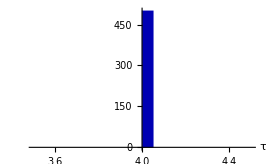
{-Graphics-,{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}}

```mathematica
hist[timeStep,Function[σ,xB[μ,σ,r,θ,k,α,δ]],0.01,μ,0.001,horizon,NsamplePaths,Darker[Blue,.3]]
```

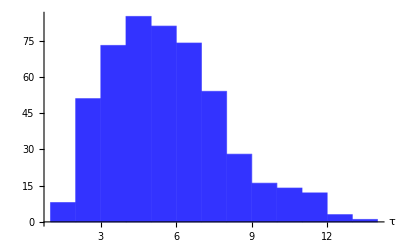
{-Graphics-,{4,2,4,6,9,5,9,4,3,4,3,3,7,5,2,4,9,3,9,7,5,11,2,8,4,5,3,2,6,4,7,4,3,6,5,6,4,3,6,4,5,7,5,5,8,5,3,3,7,7,5,4,10,5,2,4,4,8,8,6,8,9,5,2,6,7,4,6,4,5,3,3,6,6,3,7,3,4,8,7,4,6,4,4,4,8,6,2,6,2,9,3,3,6,4,5,3,5,3,6,4,4,2,5,5,3,5,3,7,2,1,5,2,10,5,6,9,1,4,2,4,6,7,7,6,8,6,5,4,5,5,3,10,8,3,5,2,3,3,5,2,4,4,4,10,7,4,3,10,4,3,6,7,3,5,4,10,13,6,4,2,5,6,6,8,4,4,5,4,3,7,1,3,3,6,5,1,3,2,4,5,5,8,4,5,6,7,7,4,4,3,6,10,6,7,4,4,5,6,4,4,8,5,2,5,3,3,6,5,7,2,1,4,7,8,5,10,6,3,5,3,5,5,1,7,5,5,7,8,4,6,9,3,8,2,6,7,2,3,7,2,5,4,6,11,11,5,7,4,2,3,3,7,6,2,5,2,5,3,5,11,3,3,4,8,6,11,2,2,6,8,8,6,4,6,12,7,8,8,2,4,5,3,7,7,4,11,2,9,4,4,5,11,4,3,7,3,2,4,2,8,6,6,11,2,5,8,7,7,4,4,7,3,8,7,10,6,5,6,2,6,7,6,2,6,4,8,10,7,4,3,6,6,3,4,2,11,3,1,7,3,9,4,9,8,2,4,4,2,2,4,6,5,3,7,6,4,2,2,4,4,4,7,5,3,3,7,6,6,5,2,5,2,3,3,7,6,1,7,6,2,3,7,5,7,2,5,6,5,5,12,11,6,2,7,3,2,4,8,7,5,4,4,9,7,4,2,5,5,5,4,6,5,9,7,6,3,10,3,3,6,3,9,4,5,2,5,3,3,6,5,4,3,10,3,3,3,3,4,6,6,6,5,6,11,5,5,11,3,4,6,5,7,4,8,5,6,2,5,6,12,5,2,4,10,6,5,6,4,7,6,7,7,4,5,6,3,6,7,2,2,9,5,3,4,3,9,5,4,5,7,6,8,3,4,6,6,5,5,10}, | Statistic | P-Value
Shapiro-Wilk | 0.950508 | 6.88092×10^-12}

```mathematica
hist[timeStep,Function[σ,xB[μ,σ,r,θ,k,α,δ]],0.01,μ,0.1,horizon,NsamplePaths,Lighter[Blue, 0.2]]
```

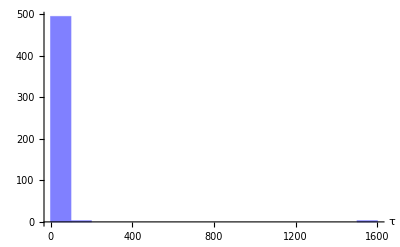
{-Graphics-,{19,23,3,55,27,28,6,6,19,39,16,7,16,3,12,9,7,4,16,10,37,6,178,10,21,29,13,10,15,19,4,51,15,19,8,6,11,43,18,45,17,36,2,29,8,5,7,3,39,17,9,19,13,4,1,25,7,13,74,16,5,34,16,13,54,14,13,6,36,14,85,8,7,6,12,11,12,20,36,4,81,3,8,15,14,5,25,14,17,4,16,14,14,10,8,17,6,10,3,14,7,13,19,16,23,19,30,8,10,28,38,37,22,31,15,17,27,16,9,28,20,12,12,19,24,23,3,40,8,14,11,16,20,76,10,24,14,38,15,20,35,40,9,18,10,5,8,11,13,6,13,3,9,25,10,22,5,23,22,27,14,12,15,41,13,7,23,8,10,8,7,11,22,30,11,23,32,6,4,4,20,6,6,8,6,4,18,46,6,3,14,24,11,16,101,29,9,27,12,28,36,18,61,18,19,7,28,20,48,42,20,31,9,11,37,7,14,45,5,7,23,15,8,21,2,10,1501,13,30,9,17,38,11,13,7,9,3,9,70,19,5,8,12,13,20,18,6,13,7,27,23,39,13,12,3,29,8,21,7,16,17,16,14,6,16,11,90,20,2,20,3,5,4,10,17,16,48,7,16,12,10,10,40,17,3,13,9,18,28,7,22,14,7,5,26,4,4,18,25,8,16,8,15,1501,24,10,10,6,30,67,33,53,16,22,9,21,48,14,12,24,16,9,12,57,27,12,7,34,8,11,23,8,11,12,15,5,6,74,5,20,16,6,16,24,8,10,25,16,5,23,6,23,14,10,8,15,4,16,8,27,27,41,15,4,11,15,32,7,23,7,97,17,4,13,7,34,24,45,11,8,8,7,18,19,15,15,15,6,17,17,27,12,15,27,17,65,26,117,79,14,19,9,19,16,7,32,14,12,21,18,18,11,11,8,13,45,37,19,19,17,34,4,15,20,36,18,39,11,16,10,30,20,77,21,22,13,8,25,62,10,16,52,15,3,32,15,8,12,12,13,19,9,14,96,27,56,7,34,3,24,20,19,5,7,34,21,11,8,17,47,26,28,4,9,25,15,32,5,26,3,9,32,12,1501,17,12,8,83,6,10,8,20,8,7,15,31,3,13,27,6}}

```mathematica
hist[timeStep,Function[σ,xB[μ,σ,r,θ,k,α,δ]],0.01,μ,0.5,horizon,NsamplePaths,Lighter[Blue, 0.5]]
```

## Prob 1I

```mathematica
d1[μ_,σ_,r_]:=1/2-μ/σ^2+Sqrt[(1/2-μ/σ^2)^2+2r/σ^2]; 
xxB[r_,μ_, σ_,θ_,k0_,α_,δ_,k_]:=d1[μ,σ,r]/(-1+d1[μ,σ,r])( δ  k + (1-  α k0)k0/r  )/(θ- α k) (r-μ)/k;
xPos[r_,μ_, σ_,θ_,k0_,α_,δ_]:=1/((-1+d1[μ,σ,r]) r θ^2)(-d1[μ,σ,r] (-2 k0 α+2 k0^2 α^2-r δ θ) (r-μ)+√((r^2 δ^2 θ^2+4 d1[μ,σ,r]^2 k0 α (-1+k0 α) (-k0 α+k0^2 α^2-r δ θ)) (r-μ)^2));
Kopt[μ_,r_,θ_,α_,δ_,x_]:=(θ x-δ(r-μ))/(2 α x);
```

### Benchmark & Capacity Optimization Models:

{xB,xC}={0.0243435,0.024042}

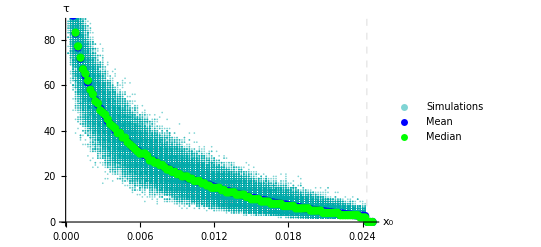
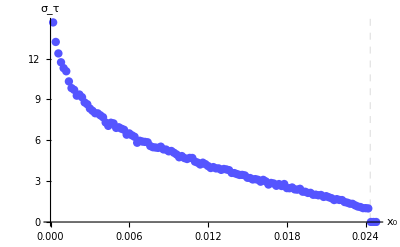
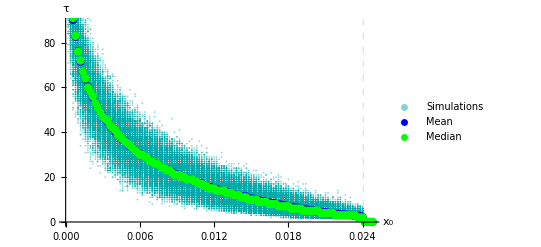
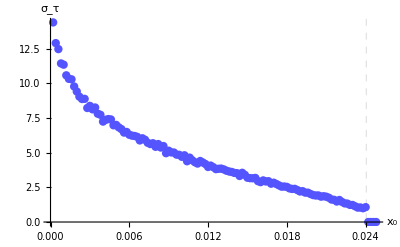

```mathematica
SeedRandom[1];
Module[
{σ=0.1,
μ=0.03,
r=0.05,
δ=2,
α=0.01,
θ=10,
k0=90,
k=100,
xStep=0.0002,
Xmin=0.0002,
Xmax,
NsamplePaths=1000,
timeStep=1,
trialBM,
trialCOM},
Print["{xB,xC}=",{xxB[r,μ, σ,θ,k0,α,δ,k],xPos[r,μ, σ,θ,k0,α,δ]}];
Xmax=Max[{xxB[r,μ, σ,θ,k0,α,δ,k],xPos[r,μ, σ,θ,k0,α,δ]}]+3*xStep;
trialBM=generalStopTime[Xmin,Xmax, xStep,NsamplePaths,timeStep,xxB[r,μ, σ,θ,k0,α,δ,k],μ,σ];
trialCOM=generalStopTime[Xmin,Xmax, xStep,NsamplePaths,timeStep,xPos[r,μ, σ,θ,k0,α,δ],μ,σ];
{Show[
(* Benchmark Model *)
(* Mean & Median *)
ListPlot[{Transpose@{Flatten@trialBM[[1]],Flatten@trialBM[[2]]},Transpose@{Mean/@trialBM[[1]],Mean/@trialBM[[2]]} ,Transpose@{Median/@trialBM[[1]],Median/@trialBM[[2]]}},
PlotStyle->{{Darker[Cyan],Opacity[.5],PointSize[0.003]},{Blue,PointSize[0.015]},{Green,PointSize[0.015]}} ,
PlotLegends->Placed[{"Simulations","Mean","Median"},{Right,Top}],
AxesLabel->{"x_0","τ"},
GridLines->{{{xxB[r,μ, σ,θ,k0,α,δ,k],Dashed}},{}}
]
],
(* Standard deviation *)
 ListPlot[Transpose@{Mean/@trialBM[[1]],StandardDeviation/@trialBM[[2]]},PlotStyle->{Lighter[Blue],PointSize[0.015]},
AxesLabel->{"x_0","σ_τ"},
GridLines->{{{xxB[r,μ, σ,θ,k0,α,δ,k],Dashed}},{}}],

(* Capacity Optimization Model *)
(* Mean & Median *)
ListPlot[{Transpose@{Flatten@trialCOM[[1]],Flatten@trialCOM[[2]]},Transpose@{Mean/@trialCOM[[1]],Mean/@trialCOM[[2]]} ,Transpose@{Median/@trialCOM[[1]],Median/@trialCOM[[2]]}},
PlotStyle->{{Darker[Cyan],Opacity[.5],PointSize[0.003]},{Blue,PointSize[0.015]},{Green,PointSize[0.015]}} ,
PlotLegends->Placed[{"Simulations","Mean","Median"},{ Right,Top}],
AxesLabel->{"x_0","τ"},
GridLines->{{{xPos[r,μ, σ,θ,k0,α,δ],Dashed}},{}}
], 
(* Standard deviation *)
 ListPlot[Transpose@{Mean/@trialCOM[[1]],StandardDeviation/@trialCOM[[2]]},PlotStyle->{Lighter[Blue],PointSize[0.015]},
AxesLabel->{"x_0","σ_τ"},
GridLines->{{{xPos[r,μ, σ,θ,k0,α,δ],Dashed}},{}}]
}
]
```

### Volatility sensibility

```mathematica
μ=0.03;
r=0.05;
δ=2;
α=0.01;
θ=10;
k=100;
k0=90;
timeStep=1;

σMax=0.5;
(* horizon=1000; 
NsamplePaths=100; *)

horizon=1500; 
NsamplePaths=500;
```

Plots para σ∈(0.001,0.5) considerando x0∈{0.001,0.01} :

```mathematica
Parallelize[ estTauB001=estTau[0.001,Function[σ,xxB[r,μ, σ,θ,k0,α,δ,k]]]];
Parallelize[ estTauB01=estTau[0.01,Function[σ,xxB[r,μ, σ,θ,k0,α,δ,k]]] ];
Parallelize[ estTauC001=estTau[0.001,Function[σ,xPos[r,μ, σ,θ,k0,α,δ]]] ];
Parallelize[ estTauC01=estTau[0.01,Function[σ,xPos[r,μ, σ,θ,k0,α,δ]]] ];
```

(σ, # unended sample paths) = {0.36,2}

(σ, # unended sample paths) = {0.37,10}

(σ, # unended sample paths) = {0.38,11}

(σ, # unended sample paths) = {0.39,24}

(σ, # unended sample paths) = {0.4,49}

(σ, # unended sample paths) = {0.41,57}

(σ, # unended sample paths) = {0.42,79}

(σ, # unended sample paths) = {0.43,123}

(σ, # unended sample paths) = {0.44,161}

(σ, # unended sample paths) = {0.45,190}

(σ, # unended sample paths) = {0.46,218}

(σ, # unended sample paths) = {0.47,256}

(σ, # unended sample paths) = {0.48,256}

(σ, # unended sample paths) = {0.49,264}

(σ, # unended sample paths) = {0.5,316}

(σ, # unended sample paths) = {0.44,2}

(σ, # unended sample paths) = {0.45,1}

(σ, # unended sample paths) = {0.46,4}

(σ, # unended sample paths) = {0.47,8}

(σ, # unended sample paths) = {0.48,12}

(σ, # unended sample paths) = {0.49,20}

(σ, # unended sample paths) = {0.5,34}

(σ, # unended sample paths) = {0.37,3}

(σ, # unended sample paths) = {0.38,15}

(σ, # unended sample paths) = {0.39,23}

(σ, # unended sample paths) = {0.4,43}

(σ, # unended sample paths) = {0.41,63}

(σ, # unended sample paths) = {0.42,88}

(σ, # unended sample paths) = {0.43,128}

(σ, # unended sample paths) = {0.44,164}

(σ, # unended sample paths) = {0.45,203}

(σ, # unended sample paths) = {0.46,221}

(σ, # unended sample paths) = {0.47,242}

(σ, # unended sample paths) = {0.48,283}

(σ, # unended sample paths) = {0.49,291}

(σ, # unended sample paths) = {0.5,298}

(σ, # unended sample paths) = {0.43,3}

(σ, # unended sample paths) = {0.44,1}

(σ, # unended sample paths) = {0.45,6}

(σ, # unended sample paths) = {0.46,4}

(σ, # unended sample paths) = {0.47,14}

(σ, # unended sample paths) = {0.48,13}

(σ, # unended sample paths) = {0.49,27}

(σ, # unended sample paths) = {0.5,32}

```mathematica
{
(* Mean optimal investment times *)
ListPlot[{Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauB001},
Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauB01},
Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauC001},
Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauC01}},
PlotLegends->Placed[{"Mean(τ_B) & x_0=0.001","Mean(τ_B) & x_0=0.01",
"Mean(τ_C) & x_0=0.001",
"Mean(τ_C) & x_0=0.01"},{Left,Top}],
AxesLabel->{"σ","Time units"},
Joined->True,
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Yellow,Darker[Yellow,0.1]},
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
],
(* Demand thresholds *)
Plot[{xxB[r,μ, σ,θ,k0,α,δ,k],xPos[r,μ, σ,θ,k0,α,δ]},{σ,0.01,σMax},
AxesOrigin->{0,0},
PlotLegends->Placed[{"x_B^*","x_C^*"},{Left,Top}],
AxesLabel->{"σ","x"}],
Plot[Kopt[μ,r,θ,α,δ,xPos[r,μ, σ,θ,k0,α,δ]],{σ,0.01,σMax},
AxesOrigin->{0,0},
AxesLabel->{"σ","K^*"},
PlotStyle->Brown],
(* % variation *)
ListPlot[
{
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTauB001,1]-Drop[estTauB001,-1])},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTauB01,1]-Drop[estTauB01,-1])},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTauC001,1]-Drop[estTauC001,-1])},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTauC01,1]-Drop[estTauC01,-1])},
Table[{σ+0.01,(xB[μ,σ+0.01,r,θ,k,α,δ]-xB[μ,σ,r,θ,k,α,δ])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(xPos[r,μ, σ+0.01,θ,k0,α,δ]-xPos[r,μ, σ,θ,k0,α,δ])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(Kopt[μ,r,θ,α,δ,xPos[r,μ, σ+0.01,θ,k0,α,δ]]-Kopt[μ,r,θ,α,δ,xPos[r,μ, σ,θ,k0,α,δ]])},{σ,0.01,σMax-0.01,0.01}]
},
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Yellow,Darker[Yellow,0.2],Lighter[Blue,0.3],Lighter[Orange,0.2],Brown},
PlotLegends->Placed[{"Mean(τ_B) & x_0=0.001","Mean(τ_B) & x_0=0.01",
"Mean(τ_C) & x_0=0.001",
"Mean(τ_C) & x_0=0.01",
"x_B^*","x_C^*","K^*" },{Left,Top}],
AxesLabel->{"σ","% variation"},
Joined->True,
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
]
}
```

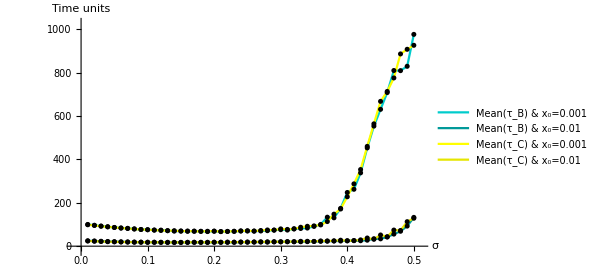
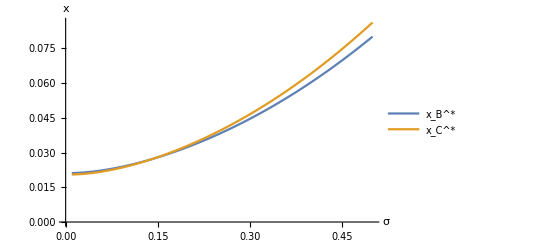
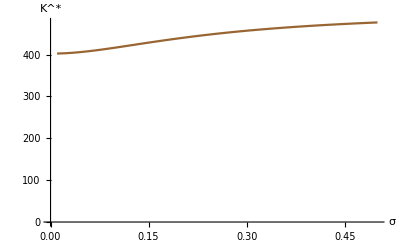
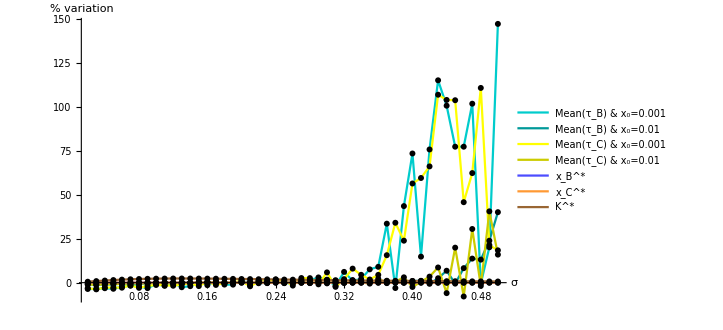

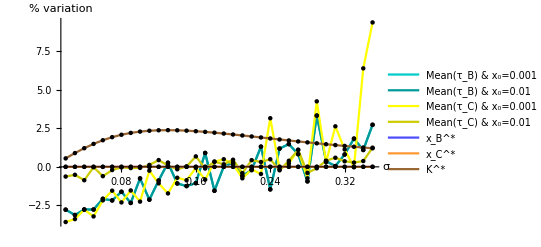

```mathematica
(* % variation up to σ=0.35 *)
Module[{σMax=0.35},
ListPlot[
{Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB001,1]-Drop[estTauB001,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB001,1]-Drop[estTauB001,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauC001,1]-Drop[estTauC001,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauC01,1]-Drop[estTauC01,-1]),(σMax-0.01)/0.01]},
Table[{σ+0.01,(xB[μ,σ+0.01,r,θ,k,α,δ]-xB[μ,σ,r,θ,k,α,δ])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(xPos[r,μ, σ+0.01,θ,k0,α,δ]-xPos[r,μ, σ,θ,k0,α,δ])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(Kopt[μ,r,θ,α,δ,xPos[r,μ, σ+0.01,θ,k0,α,δ]]-Kopt[μ,r,θ,α,δ,xPos[r,μ, σ,θ,k0,α,δ]])},{σ,0.01,σMax-0.01,0.01}]
},
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Yellow,Darker[Yellow,0.2], Lighter[Blue,0.3],Lighter[Orange,0.2],Brown},
PlotLegends->Placed[{"Mean(τ_B) & x_0=0.001","Mean(τ_B) & x_0=0.01",
"Mean(τ_C) & x_0=0.001",
"Mean(τ_C) & x_0=0.01",
"x_B^*","x_C^*","K^*" },{Scaled[{0,0.5}], {0, 0.5}}],
AxesLabel->{"σ","% variation"},
Joined->True,
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
]
]
```

Tabela representativa:

```mathematica
Δ=Table[i,{i,0.05,0.4,0.05}];
part=Table[σ,{σ,0.01,σMax,0.01}];
Grid[{
 Join[{"x_0"," σ "},Δ],
Join[{" ", "K^*"},Map[Function[σ,NumberForm[Kopt[μ,r,θ,α,δ,xPos[r,μ, σ,θ,k0,α,δ]],5]],Δ]],

Join[{" ", "x_B^*"},Map[Function[σ,NumberForm[xxB[r,μ, σ,θ,k0,α,δ,k],2]],Δ]],
Join[{" ", "x_C^*"},Map[Function[σ,NumberForm[xPos[r,μ, σ,θ,k0,α,δ],2]],Δ]],

Join[{0.001, "OverBar[τ_B]"},N@Flatten@Map[Function[elem,estTauB001[[Flatten@Position[part,elem]]]],Δ]],
Join[{0.001, "OverBar[τ_C]"},N@Flatten@Map[Function[elem,estTauC001[[Flatten@Position[part,elem]]]],Δ]],

Join[{0.01, "OverBar[τ_B]"},N@Flatten@Map[Function[elem,estTauB01[[Flatten@Position[part,elem]]]],Δ]],
Join[{0.01, "OverBar[τ_C]"},N@Flatten@Map[Function[elem,estTauC01[[Flatten@Position[part,elem]]]],Δ]]
},
Dividers->{{2->True,3->True},{1->True,2->True,-5->True,-3->True,-1->True}}
]
```

x_0 |  σ  | 0.05 | 0.1 | 0.15 | 0.2 | 0.25 | 0.3 | 0.35 | 0.4
  | K^* | 406.62 | 416.81 | 428.59 | 439.6 | 449.1 | 457.01 | 463.51 | 468.84
  | x_B^* | 0.022 | 0.024 | 0.028 | 0.033 | 0.038 | 0.045 | 0.052 | 0.06
  | x_C^* | 0.021 | 0.024 | 0.028 | 0.033 | 0.039 | 0.047 | 0.055 | 0.064
0.001 | OverBar[τ_B] | 67.64 | 58.706 | 53.644 | 52.224 | 52.46 | 57.49 | 63.972 | 106.982
0.001 | OverBar[τ_C] | 78.21 | 68.426 | 63.82 | 63.938 | 65.552 | 70.664 | 90.086 | 193.648
0.01 | OverBar[τ_B] | 4.294 | 5.258 | 6.478 | 7.814 | 9.532 | 10.254 | 11.902 | 14.154
0.01 | OverBar[τ_C] | 13.884 | 12.892 | 13.4 | 14.924 | 15.526 | 16.93 | 19.768 | 23.112

## Prob III

```mathematica
d1[μ_,σ_,r_]:=1/2-μ/σ^2+Sqrt[(1/2-μ/σ^2)^2+2r/σ^2]; 

xxB1[r_,μ_, σ_,θ_,k0_,α_,δ_,k_,η_]:=d1[μ,σ,r]/(-1+d1[μ,σ,r])(δ k(r-μ))/((θ- α k) k -2η k0 k); (* x_1,A *) 
xxB2[r_,μ_, σ_,θ_,k0_,α_,δ_,k_,η_]:=(d1[μ,σ,r] (1-k0 α) (r-μ))/(2 (-1+d1[μ,σ,r] ) k r η); (* x_2 *)
xxB[r_,μ_, σ_,θ_,k0_,α_,δ_,k_]:=d1[μ,σ,r]/(-1+d1[μ,σ,r])( δ  k + (1-  α k0)k0/r  )/(θ- α k) (r-μ)/k; (* x_1,R ; não utilizada para análise -> Prob II *)
```

### Benchmark Model with 2 stopping times (simultaneous prod & replace) :

```mathematica
SeedRandom[1];
Module[
{σ=0.1,
μ=0.45,
r=0.85,
δ=0.95,
α=0.015,
θ=1.5,
k0=51.5,
k=2.5,
xStep=0.002,
Xmin=0.002,
Xmax,
NsamplePaths=1000,
timeStep=1,
(* η={0.007,0.012,0.013},*)
trialBM,
trialBM2,
η=0.007},
If[η<(1-α k0)(θ-α k)/(2(δ k r+ (1-α k0)k0)) (* η* *),
Print["Existe produção simultânea, logo dois tempos de paragem."],
Print["Não existe produção simultânea, logo um único tempo de paragem - ver Prob II."]
];
Print["{x1A,x2,x1R}=",{xxB1[r,μ, σ,θ,k0,α,δ,k,η],xxB2[r,μ, σ,θ,k0,α,δ,k,η],xxB[r,μ, σ,θ,k0,α,δ,k]}];
Xmax=xxB1[r,μ, σ,θ,k0,α,δ,k,η]+10*xStep;
trialBM=generalStopTime[Xmin,Xmax, xStep,NsamplePaths,timeStep,xxB1[r,μ, σ,θ,k0,α,δ,k,η],μ,σ];
trialBM2=generalStopTime[xxB1[r,μ, σ,θ,k0,α,δ,k,η],xxB1[r,μ, σ,θ,k0,α,δ,k,η], xStep,NsamplePaths,timeStep,xxB2[r,μ, σ,θ,k0,α,δ,k,η],μ,σ];
{
(* First stopping time *)
(* Mean & Median *)
ListPlot[{Transpose@{Flatten@trialBM[[1]],Flatten@trialBM[[2]]},Transpose@{Mean/@trialBM[[1]],Mean/@trialBM[[2]]} ,Transpose@{Median/@trialBM[[1]],Median/@trialBM[[2]]}},
PlotStyle->{{Darker[Cyan],Opacity[.5],PointSize[0.003]},{Blue,PointSize[0.015]},{Green,PointSize[0.015]}} ,
PlotLegends->Placed[{"Simulations","Mean","Median"},{Right,Top}],
AxesLabel->{"x_0","τ"},
PlotRange->All,
GridLines->{{{xxB1[r,μ, σ,θ,k0,α,δ,k,η],Dashed}},{}}
],
(* Standard deviation *)
ListPlot[Transpose@{Mean/@trialBM[[1]],StandardDeviation/@trialBM[[2]]},PlotStyle->{Lighter[Blue],PointSize[0.015]},
AxesLabel->{"x_0","σ_τ"},
GridLines->{{{xxB1[r,μ, σ,θ,k0,α,δ,k,η],Dashed}},{}}],
(* Second stopping time *)
Grid[{{" ","τ_2"," "},
{(* "x_(1, A)^*","x_2^*",*) "Mean" ,"Median","Std. Dev."},
{Mean@trialBM2[[2,1]],Median@trialBM2[[2,1]],StandardDeviation@trialBM[[2,1]]} 
},
Dividers->{{},{1->True,2->True,-1->True}} 
]
}
]
```

Existe produção simultânea, logo dois tempos de paragem.

{x1A,x2,x1R}={1.10099,6.57153,3.79792}

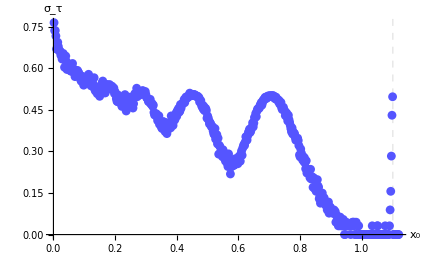
```mathematica
{-Graphics-,-Graphics-,{{" ", "\!\(\*SubscriptBox[\(τ\), \(2\)]\)", " "}, {"Mean", "Median", "Std. Dev."}, {5.486000000000121, 5.0009999999999994, 0.7651152863467048}}}
```

### Volatility sensibility

```mathematica
μ=0.45;
r=0.85;
δ=0.95;
α=0.015;
θ=1.5;
k0=51.5;
k=2.5;
η=0.007;
timeStep=1;

σMax=0.5;
(* horizon=1000; 
NsamplePaths=100; *)

horizon=1500; 
NsamplePaths=500;
```

Plots para σ∈(0.001,0.5) considerando x0∈{0.001,0.01} :

```mathematica
estTauB001=estTau[0.001,Function[σ,xxB1[r,μ, σ,θ,k0,α,δ,k,η]]];
estTauB01=estTau[0.01,Function[σ,xxB1[r,μ, σ,θ,k0,α,δ,k,η]]];
estTauB2=Table[
b =Table[
stopTimemod[timeStep,xxB2[r,μ, σ,θ,k0,α,δ,k,η],xxB1[r,μ, σ,θ,k0,α,δ,k,η],μ,σ,horizon],{i,NsamplePaths}];
If[Count[First/@b,horizon+timeStep] >0,
Print["(σ_B, # unended sample paths) = ",{σ,Count[First/@b,horizon+timeStep]}]
];
Mean[First/@b],
{σ,0.01,σMax,0.01}];
```

```mathematica
{
(* Mean optimal investment times *)
ListPlot[{Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauB001},
Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauB01},
Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauB2}},
PlotLegends->Placed[{"Mean(τ_B) & x_0=0.001","Mean(τ_B) & x_0=0.01",
"Mean(τ_2)"},{Left,Top}],
AxesLabel->{"σ","Time units"},
Joined->True,
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Darker[Green,0.1]},
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
],
(* Demand thresholds *)
Plot[{xxB1[r,μ, σ,θ,k0,α,δ,k,η],xxB2[r,μ, σ,θ,k0,α,δ,k,η]},{σ,0.01,σMax},
AxesOrigin->{0,0},
PlotLegends->Placed[{"x_(1, A)^*","x_2^*"},{Left,Top}],
AxesLabel->{"σ","x"}],
(* % variation *)
ListPlot[
{
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB001,1]-Drop[estTauB001,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB01,1]-Drop[estTauB01,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB2,1]-Drop[estTauB2,-1]),(σMax-0.01)/0.01]},
Table[{σ+0.01,(xxB1[r,μ, σ+0.01,θ,k0,α,δ,k,η]-xxB1[r,μ, σ,θ,k0,α,δ,k,η])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(xxB2[r,μ, σ+0.01,θ,k0,α,δ,k,η]-xxB2[r,μ, σ,θ,k0,α,δ,k,η])},{σ,0.01,σMax-0.01,0.01}]
},
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Darker[Green,0.1], Lighter[Blue,0.3],Lighter[Orange,0.2]},
PlotLegends->Placed[{"Mean(τ_(1, A)) & x_0=0.001","Mean(τ_(1, A)) & x_0=0.01",
"Mean(τ_2)","x_(1, A)^*","x_2^*"},{Left,Bottom}],
AxesLabel->{"σ","% variation"},
Joined->True,
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
]
}
```

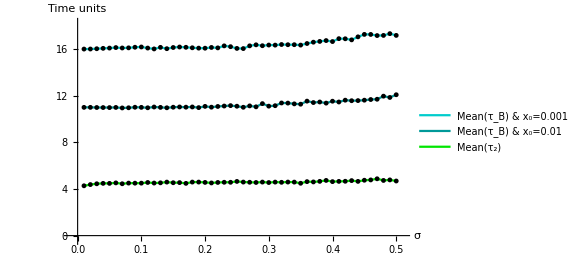
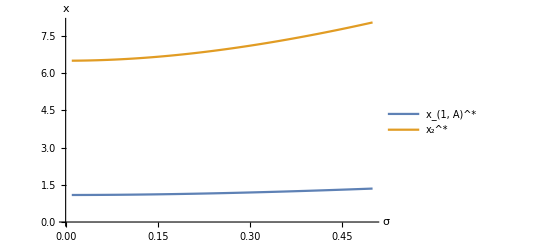
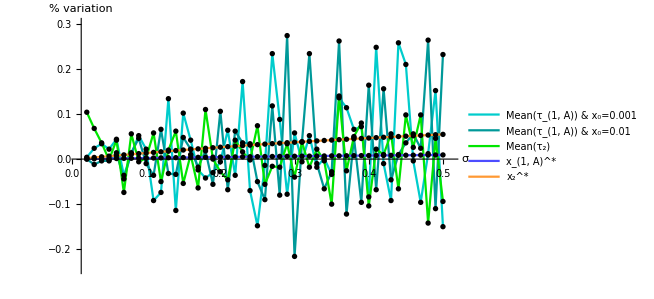

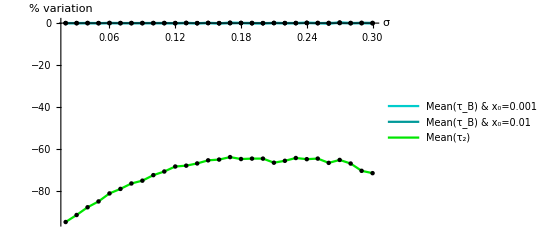

```mathematica
(* % varitation up to σ=0.3 *)
Module[{σMax=0.30},
ListPlot[
 {Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB001,1]-Drop[estTauB001,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB01,1]-Drop[estTauB01,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB2,1]-Drop[estTauC001,-1]),(σMax-0.01)/0.01]},
Table[{σ+0.01,(xxB1[r,μ, σ+0,01,θ,k0,α,δ,k,η]-xxB1[r,μ, σ,θ,k0,α,δ,k,η])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(xxB2[r,μ, σ+0.01,θ,k0,α,δ,k,η]-xxB2[r,μ, σ,θ,k0,α,δ,k,η])},{σ,0.01,σMax-0.01,0.01}]
},
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Darker[Green,0.1]},
PlotLegends->Placed[{"Mean(τ_B) & x_0=0.001","Mean(τ_B) & x_0=0.01",
"Mean(τ_2)" },,{Scaled[{0,0.5}], {0, 0.5}}],
AxesLabel->{"σ","% variation"},
Joined->True,
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
]
]
```

Tabela representativa:

```mathematica
Δ=Table[i,{i,0.05,0.4,0.05}];
part=Table[σ,{σ,0.01,σMax,0.01}];
Grid[{
 Join[{"x_0"," σ "},Δ],

Join[{" ", "x_(1, A)^*"},Map[Function[σ,NumberForm[xxB1[r,μ, σ,θ,k0,α,δ,k,η],2]],Δ]],
Join[{" ", "x_2^*"},Map[Function[σ,NumberForm[xxB2[r,μ, σ,θ,k0,α,δ,k,η],2]],Δ]],

Join[{0.001, "OverBar[τ_(1, A)]"},N@Flatten@Map[Function[elem,estTauB001[[Flatten@Position[part,elem]]]],Δ]],
Join[{0.01, "OverBar[τ_(1, A)]"},N@Flatten@Map[Function[elem,estTauB01[[Flatten@Position[part,elem]]]],Δ]],

Join[{" ", "OverBar[τ_2]"},N@Flatten@Map[Function[elem,estTauB2[[Flatten@Position[part,elem]]]],Δ]]
},
Dividers->{{2->True,3->True},{1->True,2->True,-4->True,-2->True,-1->True}}
]
```

x_0 |  σ  | 0.05 | 0.1 | 0.15 | 0.2 | 0.25 | 0.3 | 0.35 | 0.4
  | x_(1, A)^* | 1.1 | 1.1 | 1.1 | 1.1 | 1.2 | 1.2 | 1.2 | 1.3
  | x_2^* | 6.5 | 6.6 | 6.7 | 6.8 | 6.9 | 7.1 | 7.3 | 7.5
0.001 | OverBar[τ_(1, A)] | 16.084 | 16.178 | 16.134 | 16.074 | 16.056 | 16.344 | 16.34 | 16.644
0.01 | OverBar[τ_(1, A)] | 10.98 | 11. | 11.012 | 11.084 | 11.098 | 11.104 | 11.272 | 11.528
  | OverBar[τ_2] | 4.48 | 4.5 | 4.536 | 4.564 | 4.648 | 4.552 | 4.49 | 4.63

### Histograma

```mathematica
μ=0.45;
r=0.85;
δ=0.95;
α=0.015;
θ=1.5;
k0=51.5;
k=2.5;
η=0.007;
timeStep=1;

σMax=0.5;
(* horizon=1000; 
NsamplePaths=100; *)

horizon=1500; 
NsamplePaths=500;
```

```mathematica
hist[timeStep_,xfunc_,x0_,μ_,σ_,horizon_,NsamplePaths_,color_]
```

#### x = 0.001

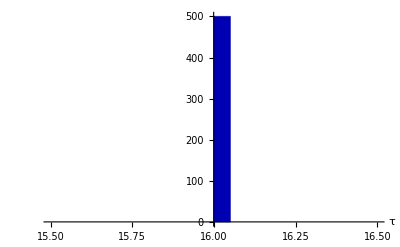
{-Graphics-,{16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16}, | Statistic | P-Value
Shapiro-Wilk | ComplexInfinity | 0.}

```mathematica
hist[timeStep,Function[σ,xxB1[r,μ, σ,θ,k0,α,δ,k,η]],0.001,μ,0.001,horizon,NsamplePaths,Darker[Blue,.3]]
```

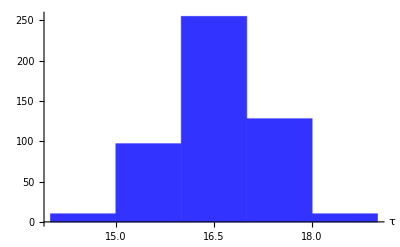
{-Graphics-,{15,17,15,16,16,16,17,16,14,16,17,16,16,16,16,16,15,17,16,16,17,16,17,16,17,16,15,17,16,15,15,16,16,17,17,16,16,17,15,17,16,17,17,15,17,14,16,16,16,16,16,15,15,15,15,15,16,17,16,16,17,16,17,15,16,15,17,17,16,16,15,17,15,16,15,16,16,16,16,16,15,16,17,16,15,16,16,16,15,17,16,16,17,15,17,17,16,16,16,16,17,16,17,16,15,15,16,16,16,16,16,14,16,17,16,16,17,17,15,18,16,15,16,17,16,15,16,16,16,17,16,17,15,16,16,17,16,16,16,17,15,15,15,17,16,16,17,16,17,16,16,16,15,17,16,16,17,16,15,15,15,16,15,17,16,16,16,16,16,15,17,15,16,17,16,17,16,17,16,17,17,15,16,15,17,16,15,17,17,16,15,16,18,16,17,16,15,16,17,17,16,15,16,14,18,17,16,15,16,17,15,17,16,16,17,17,16,16,16,16,17,16,17,16,16,17,17,14,17,16,17,16,16,15,16,16,16,16,16,17,16,18,16,15,16,17,17,15,16,17,16,16,16,17,16,16,15,16,17,16,16,16,15,15,16,17,16,16,17,16,15,17,16,17,17,16,16,17,18,18,18,16,15,15,15,16,16,16,16,15,15,18,16,15,16,14,15,16,16,16,17,16,16,17,16,16,16,18,16,15,16,16,18,16,16,17,16,16,15,16,16,16,17,17,16,17,16,17,17,17,15,15,16,16,17,15,16,17,17,16,16,16,16,16,17,16,17,15,16,16,16,17,15,16,16,17,17,16,16,15,15,17,17,16,16,17,16,15,15,16,17,16,16,15,17,17,15,17,16,16,15,16,16,17,16,16,16,16,15,15,17,16,16,16,15,17,16,16,17,15,16,17,17,16,16,16,17,16,16,16,16,16,16,16,16,17,17,16,17,16,15,16,16,16,16,15,16,15,15,16,16,15,15,16,16,17,17,15,17,16,16,17,16,15,16,16,15,17,17,14,16,16,14,16,16,16,17,16,15,16,17,16,17,16,15,17,16,16,15,16,16,16,14,17,16,16,17,17,15,16,16,16,15,15,15,16,15,17,14,15,16,16,16,16,16,17,17,15,16,17}, | Statistic | P-Value
Shapiro-Wilk | 0.86116 | 1.23252×10^-20}

```mathematica
hist[timeStep,Function[σ,xxB1[r,μ, σ,θ,k0,α,δ,k,η]],0.001,μ,0.1,horizon,NsamplePaths,Lighter[Blue, 0.2]]
```

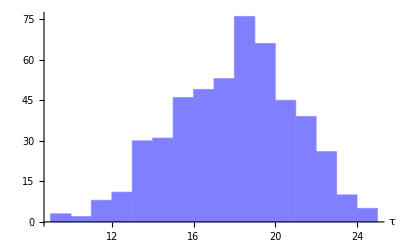
{-Graphics-,{15,16,23,21,18,13,18,17,19,14,14,19,18,15,18,18,13,17,17,17,19,13,14,19,18,18,18,16,21,18,15,18,24,20,17,18,18,17,13,15,17,22,11,14,15,18,12,16,18,15,19,18,19,17,19,15,19,15,19,17,14,16,15,15,21,16,20,22,20,18,15,20,22,18,16,20,20,15,20,23,15,22,20,18,14,18,18,15,21,15,13,17,17,16,13,19,21,12,20,21,18,14,22,23,15,16,21,19,18,18,12,13,18,14,15,19,19,19,17,17,17,12,13,18,24,19,17,13,18,22,21,13,19,16,14,17,18,19,19,18,19,20,20,17,12,15,19,20,21,18,19,17,18,18,16,15,22,18,18,20,16,14,12,19,16,17,14,21,20,12,19,22,20,18,23,15,13,16,15,19,18,22,20,18,19,11,17,19,20,14,21,18,20,19,18,13,11,20,15,16,11,17,19,18,15,18,18,21,9,19,15,13,14,15,12,23,13,13,16,14,20,18,11,19,21,23,14,19,17,14,18,19,21,20,21,17,19,16,10,17,20,12,18,19,16,21,11,22,19,17,21,19,17,19,16,21,14,22,18,17,16,17,21,19,19,16,16,14,13,16,16,22,20,16,18,16,18,20,20,16,19,20,13,21,20,15,21,13,20,18,18,9,22,23,13,13,13,19,24,21,16,22,19,21,15,21,16,23,18,22,15,14,19,14,17,16,22,21,14,20,20,22,15,15,20,17,19,21,13,22,18,14,20,14,18,16,17,16,15,17,17,22,13,13,19,16,22,19,20,16,18,18,18,19,14,14,14,16,17,20,15,17,21,22,19,18,20,23,15,18,17,15,16,18,11,13,18,22,19,15,20,20,13,21,17,20,19,15,17,22,12,21,18,17,19,18,24,13,17,19,17,16,15,17,19,15,21,16,19,14,20,21,19,17,13,17,16,9,21,17,17,18,19,18,15,19,20,16,18,15,21,16,20,19,17,18,15,21,19,13,17,21,12,18,16,19,19,15,18,20,20,16,18,14,20,15,20,16,18,19,16,14,14,17,19,16,23,18,19,22,21,18,18,18,18,17,16,16,22,21,22,19,17,13,17,16,19,21,14,15,18,15,11,17,18,24,16,15,21,10}, | Statistic | P-Value
Shapiro-Wilk | 0.982461 | 9.91904×10^-6}

```mathematica
hist[timeStep,Function[σ,xxB1[r,μ, σ,θ,k0,α,δ,k,η]],0.001,μ,0.5,horizon,NsamplePaths,Lighter[Blue, 0.5]]
```

#### x = 0.01

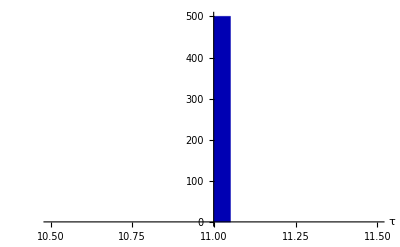
{-Graphics-,{11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11}, | Statistic | P-Value
Shapiro-Wilk | ComplexInfinity | 0.}

```mathematica
hist[timeStep,Function[σ,xxB1[r,μ, σ,θ,k0,α,δ,k,η]],0.01,μ,0.001,horizon,NsamplePaths,Darker[Blue,.3]]
```

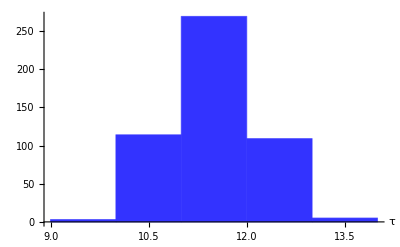
{-Graphics-,{12,10,12,10,11,12,10,12,11,12,10,11,11,10,11,10,11,10,11,10,11,10,11,12,12,10,12,11,11,12,11,11,11,11,11,11,10,10,10,11,10,11,12,11,10,11,11,10,11,11,13,11,11,11,10,11,11,11,11,10,11,11,11,11,11,11,11,13,10,12,12,11,10,11,12,11,11,11,12,12,11,10,11,11,11,12,12,11,10,12,11,11,11,10,11,11,11,11,10,12,11,10,12,11,11,11,11,13,11,12,10,11,11,11,12,11,12,10,12,10,11,11,10,11,11,11,10,11,10,11,11,10,12,12,12,11,11,11,10,12,11,10,11,11,11,12,12,9,12,10,11,11,11,11,11,11,11,10,12,12,11,10,12,11,11,12,11,11,11,11,12,12,11,10,11,10,11,11,12,11,12,11,12,12,11,11,10,10,11,12,12,10,11,11,11,11,12,10,11,11,12,11,11,11,11,11,11,11,12,10,10,11,11,11,10,11,10,10,10,10,10,11,10,11,12,11,11,10,12,11,11,11,10,11,11,11,11,12,10,12,11,11,11,11,11,11,11,11,11,12,11,11,11,11,11,10,11,11,12,10,11,12,10,11,12,12,10,10,11,11,10,11,10,10,10,10,11,10,12,11,12,11,11,10,12,11,11,11,11,11,11,11,12,13,12,10,12,10,12,10,11,12,11,11,11,10,11,10,11,11,10,10,10,11,10,10,10,11,11,10,11,11,11,12,11,11,11,11,11,11,12,11,10,11,11,12,11,11,11,12,12,10,11,11,12,10,11,10,10,10,11,11,11,12,11,11,11,10,12,11,11,11,10,12,11,12,11,12,11,10,11,10,12,10,11,10,10,11,10,10,11,11,12,10,11,13,11,11,12,12,12,10,10,12,11,11,11,11,12,10,11,11,11,11,12,11,11,12,11,11,10,12,11,11,12,11,10,12,11,10,11,9,10,9,11,11,11,11,11,10,10,12,11,12,11,12,12,11,12,12,10,10,12,12,12,10,11,12,11,11,10,11,12,12,11,10,11,11,11,11,10,10,12,10,12,11,11,11,11,11,11,11,11,10,11,11,12,12,12,12,12,11,11,11,11,11,12,11,12,11,11,11,10,11,11,11,12,11,12,11}, | Statistic | P-Value
Shapiro-Wilk | 0.834896 | 2.30754×10^-22}

```mathematica
hist[timeStep,Function[σ,xxB1[r,μ, σ,θ,k0,α,δ,k,η]],0.01,μ,0.1,horizon,NsamplePaths,Lighter[Blue, 0.2]]
```

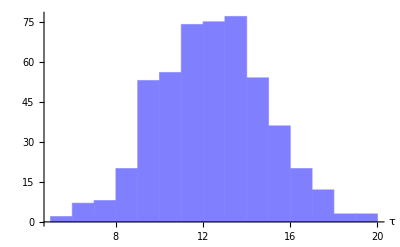
{-Graphics-,{9,12,12,13,13,8,6,15,12,10,10,9,9,11,11,13,11,13,15,18,11,14,13,10,16,7,11,11,12,13,8,8,9,16,13,9,14,19,11,10,14,12,12,11,10,13,11,10,13,6,13,11,11,11,15,15,9,9,13,13,14,8,12,15,12,9,16,14,13,12,12,17,10,13,13,12,10,10,10,9,11,14,10,7,14,17,16,11,12,13,13,15,13,16,12,13,13,13,10,10,10,9,12,15,9,11,9,11,14,10,12,10,12,10,11,9,14,14,10,10,14,13,6,11,11,11,13,14,14,14,11,8,14,5,14,12,16,12,13,11,13,13,12,10,15,11,13,10,16,17,8,6,11,12,13,9,15,9,18,10,12,9,13,8,10,10,13,13,9,13,11,11,14,14,11,15,14,7,13,13,11,12,11,14,13,13,11,14,12,14,12,14,12,9,17,12,12,12,13,13,11,16,12,11,13,9,14,14,12,11,10,12,12,14,15,15,10,13,15,13,12,12,9,9,11,15,11,12,11,12,11,13,14,10,10,14,10,15,15,15,10,10,10,14,11,11,12,16,13,9,14,9,9,15,11,13,11,16,9,10,14,12,8,12,9,12,12,8,11,12,12,11,10,14,12,6,13,15,13,11,14,13,9,9,15,17,12,11,14,11,16,14,15,11,12,8,9,8,11,12,15,10,13,13,16,14,9,7,15,13,15,11,13,13,9,11,11,14,11,14,10,11,7,12,10,7,16,12,12,13,17,9,11,10,12,14,13,12,17,10,12,12,13,9,16,15,16,9,13,7,13,14,12,11,17,8,13,12,18,11,10,14,10,9,9,15,13,11,13,13,9,10,15,8,9,10,19,15,11,15,11,11,9,10,9,10,7,8,9,11,5,15,12,11,12,11,8,14,14,9,16,12,9,11,9,11,15,12,14,11,15,17,12,16,8,12,13,15,11,15,11,13,13,13,10,16,13,9,8,9,17,13,11,9,9,12,12,17,15,12,13,9,13,13,11,10,12,11,16,14,12,14,10,13,12,10,13,12,14,12,11,13,14,15,6,16,14,12,12,13,13,10,9,13,9,19,10,11,9,8,12,11,10,14,10,12,8,13,10,17,10,14,6,14,14,12,8,10,9,14}, | Statistic | P-Value
Shapiro-Wilk | 0.984902 | 0.0000468446}

```mathematica
hist[timeStep,Function[σ,xxB1[r,μ, σ,θ,k0,α,δ,k,η]],0.01,μ,0.5,horizon,NsamplePaths,Lighter[Blue, 0.5]]
```